```mathematica
ClearAll["Global`*"]
```

```mathematica
norm[θ_]:=θ-2π Floor[θ/(2π)]
```

```mathematica
n=10;
```

```mathematica
(*check U*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_sm_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

```mathematica
Min[Table[t[[i,2]],{i,1,Length[t]}]]
Max[Table[t[[i,2]],{i,1,Length[t]}]]
Min[Table[t[[i,3]],{i,1,Length[t]}]]
Max[Table[t[[i,3]],{i,1,Length[t]}]]
```

-0.000231799

0.000231737

-0.000459479

-7.93352×10^-7

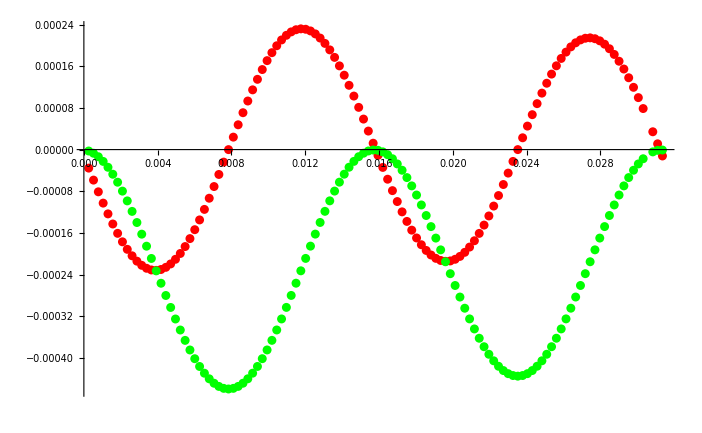

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

```mathematica
(*check nu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/nu_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

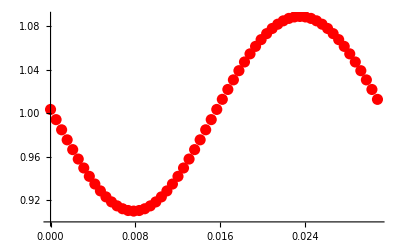

```mathematica
plotnumν=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check psi*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/dpsi_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],norm[t[[i,1]]]},{i,2,Length[t]}]
```

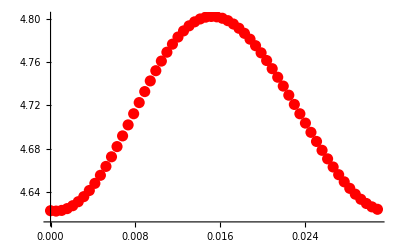

```mathematica
plotnumψ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check mu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/mu_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.014634,100.644},{0.0167246,100.552},{0.0135887,100.529},{0.0177698,100.386},{0.0125434,100.308},{0.0188151,100.182},{0.0114981,100.013},{0.0198604,99.9726},{0.0104528,99.6986},{0.0209057,99.7879},{0.00940756,99.4326},{0.021951,99.6504},{0.00836228,99.2783},{0.0229963,99.5765},{0.00731699,99.2746},{0.0240415,99.5746},{0.00627171,99.4228},{0.0250868,99.6457},{0.00522642,99.6861},{0.0261321,99.7824},{0.00418114,100.002},{0.0271774,99.9691},{0.00313585,100.302},{0.0282227,100.182},{0.00209057,100.529},{0.029268,100.391},{0.00104528,100.65},{0.0303133,100.56},{0.0313585,100.655}}

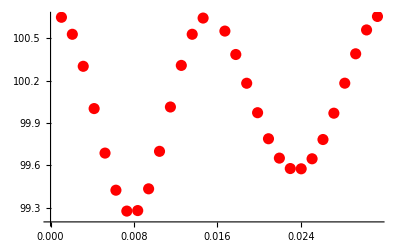

```mathematica
plotnumμ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```